# SHOT for Mathematica

This implementation of the extended supporting hyperplane (ESH) and extended cutting plane (ECP) algorithms for solving convex mixed-integer nonlinear programming (MINLP) problems is made by Andreas Lundell, andreas.lundell@abo.fi.

The supporting hyperplane optimization toolkit (SHOT) solver is described in the journal paper

	Jan Kronqvist, Andreas Lundell and Tapio Westerlund, The extended supporting hyperplane algorithm for convex mixed-integer nonlinear programming, Journal of Global Optimization 64 (2), DOI: 10.1007/s10898-015-0322-3 2015.
	
If you use this solver, please cite the paper above. 

The SHOT solver consists of two Mathematica applications. The first is the main solver contained in the file SHOT.m and the second is contained in the file OSiLReader.m, and is a parser for the OSiL format, which is an XML-based file format for optimization problems. The second is not strictly required, and it is possible to input problems manually in Mathematica syntax as well.

Note that the performance of this solver is not as good as for the C++ version detailed in the paper above. The main reason for this is due to the fact that the LinearProgramming solver used to solve the mixed-integer linear programming (MILP) subproblems in Mathematica is not as efficient as those used in the other implementation.

## Installation

The package files should be put in a place where Mathematica can find them. You can e.g. open the files OSiLReader.m and SHOT.m and on each select Install from the File-menu. You should then be able to read the packages with the commands

```mathematica
<<SHOT`OSiLReader`
<<SHOT`SHOT`
```

After installation you should check that you can use the functions available

```mathematica
?OSiLReader`*
```

```mathematica
?SHOT`*
```

## Importing OSiL

### From a file

To import an optimization problem contained in an OSiL-file, you should use the OSiLReader`ImportProblemFromOSiLFile function:

```mathematica
?OSiLReader`ImportProblemFromOSiLFile
```

ImportProblemFromOSiLFile[filename, directory, reformulate] imports the problem in OSiL format from filename in directory. The paramter reformulate parameter is True/False and indicates whether a possible nonlinear objective function should be rewritten as a constraint.

Remember to use double backslashes instead of single slashes in the path. So to import the file alan.osil in the current notebook directory use

```mathematica
{objective,linearConstraints,nonlinearConstraints,variableBounds,integerVariables,variables,objectiveDirection}=OSiLReader`ImportProblemFromOSiLFile["alan.osil",NotebookDirectory[],True,NegativeNonlinearObjectiveBound->-10000,PositiveNonlinearObjectiveBound->10000]
```

{addobjvar,{1. x1+1. x2+1. x3+1. x4==1.,8. x1+9. x2+12. x3+7. x4==10.,-1. b6+1. x1≤0.,-1. b7+1. x2≤0.,-1. b8+1. x3≤0.,-1. b9+1. x4≤0.,1. b6+1. b7+1. b8+1. b9≤3.},{0.-addobjvar+4. x1^2+6. x1 x2+6. x2^2-2. x1 x3+2. x2 x3+10. x3^2≤0},{0.≤x1≤∞,0.≤x2≤∞,0.≤x3≤∞,0.≤x4≤∞,0≤b6≤1.,0≤b7≤1.,0≤b8≤1.,0≤b9≤1.,-10000≤addobjvar≤10000},{b6∈Integers,b7∈Integers,b8∈Integers,b9∈Integers},{x1,x2,x3,x4,b6,b7,b8,b9,addobjvar},min}

Since the problem has a nonlinear objective function, and the reformulate parameter is set to true, the imported optimization problem will have an additional objective constraint and an objective function consisting of an auxilliary variable (addobjvar) only. The bounds for this parameter can be set using the options NegativeNonlinearObjectiveBound and PositiveNonlinearObjectiveBound respectively. Do not use to big values for the bounds, as it can in some cases make Mathematica’s NLP solver unstable.

### From a string or the web

It is also possible to import OSiL-files given as a string. This way you can e.g. get the file from the MINLPLib2 website without downloading it separately

```mathematica
osil=Import["http://www.gamsworld.org/minlp/minlplib2/data/osil/alan.osil","XML"];
```

```mathematica
{objective,linearConstraints,nonlinearConstraints,variableBounds,integerVariables,variables,objectiveDirection}=OSiLReader`ImportProblemFromOSiL[osil,True,NegativeNonlinearObjectiveBound->-10000,PositiveNonlinearObjectiveBound->10000]
```

{addobjvar,{1. x1+1. x2+1. x3+1. x4==1.,8. x1+9. x2+12. x3+7. x4==10.,-1. b6+1. x1≤0.,-1. b7+1. x2≤0.,-1. b8+1. x3≤0.,-1. b9+1. x4≤0.,1. b6+1. b7+1. b8+1. b9≤3.},{0.-addobjvar+4. x1^2+6. x1 x2+6. x2^2-2. x1 x3+2. x2 x3+10. x3^2≤0},{0.≤x1≤∞,0.≤x2≤∞,0.≤x3≤∞,0.≤x4≤∞,0≤b6≤1.,0≤b7≤1.,0≤b8≤1.,0≤b9≤1.,-10000≤addobjvar≤10000},{b6∈Integers,b7∈Integers,b8∈Integers,b9∈Integers},{x1,x2,x3,x4,b6,b7,b8,b9,addobjvar},min}

## Solving an optimization problem using SHOT

SHOT can solve convex mixed-integer nonlinear programming (MINLP) problems to global optimality. It can also solve continous convex nonlinear programming (NLP) problems.

To solve the problem alan.osil imported in the previous section we can use the command:

```mathematica
SHOT`SolveMINLP[objective, Join[linearConstraints,variableBounds],nonlinearConstraints,integerVariables, variables,objectiveDirection]
```

{2.925,{x1→0.375,x2→0.,x3→0.525,x4→0.0999997,b6→1.,b7→0.,b8→1.,b9→1.,addobjvar→2.925}}

Note that the variable bound constraints are to be included with the normal linear constraints, and therefore the Join command is used. The objective function value is returned together with the solution for the variables if a solution is found.

During runtime, solution info is printed to the Messages-notebook (Windows - Messages). If the PrintDebug command is used additional debug information is printed there as well:

```mathematica
SHOT`SolveMINLP[objective, Join[linearConstraints,variableBounds],nonlinearConstraints,integerVariables, variables,objectiveDirection]//PrintDebug
```

{2.925,{x1→0.375,x2→0.,x3→0.525,x4→0.0999997,b6→1.,b7→0.,b8→1.,b9→1.,addobjvar→2.925}}

Now we can try to solve the problem usingone of Mathematica’s own solvers. Note that we import the problem again, this time without reformulating it as it is not necessary in this case.

```mathematica
{objective,linearConstraints,nonlinearConstraints,variableBounds,integerVariables,variables,objectiveDirection}=OSiLReader`ImportProblemFromOSiL[osil,False]
constraints = And@@Join[linearConstraints,nonlinearConstraints,variableBounds,integerVariables];
NMinimize[{objective,constraints},variables]
```

{0.+4. x1^2+6. x1 x2+6. x2^2-2. x1 x3+2. x2 x3+10. x3^2,{1. x1+1. x2+1. x3+1. x4==1.,8. x1+9. x2+12. x3+7. x4==10.,-1. b6+1. x1≤0.,-1. b7+1. x2≤0.,-1. b8+1. x3≤0.,-1. b9+1. x4≤0.,1. b6+1. b7+1. b8+1. b9≤3.},{},{0.≤x1≤∞,0.≤x2≤∞,0.≤x3≤∞,0.≤x4≤∞,0≤b6≤1.,0≤b7≤1.,0≤b8≤1.,0≤b9≤1.},{b6∈Integers,b7∈Integers,b8∈Integers,b9∈Integers},{x1,x2,x3,x4,b6,b7,b8,b9},min}

NMinimize::incst: NMinimize was unable to generate any initial points satisfying the inequality constraints {-3. + 1.\ Round[b6] + 1.\ Round[b7] + 1.\ Round[b8] + 1.\ Round[b9] ≤ 0, 0.  + 1.\ x1 - 1.\ Round[b6] ≤ 0, 0.  + 1.\ (0.4  - 0.8\ x1 - 0.6\ x2) - 1.\ Round[b9] ≤ 0, 0.  + 1.\ (0.6  - 0.2\ x1 - 0.4\ x2) - 1.\ Round[b8] ≤ 0, -0.6 + 0.2\ x1 + 0.4\ x2 ≤ 0, -0.4 + 0.8\ x1 + 0.6\ x2 ≤ 0, 0.  + 1.\ x2 - 1.\ Round[b7] ≤ 0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

{2.925,{x1→0.37497,x2→1.49644×10^-9,x3→0.525006,x4→0.100024,b6→1,b7→0,b8→1,b9→1}}

Note that the NMinimize solver is not a global one, and although it complains about not finding an initial point it still manages to find the correct solution. This is however a relatively easy problem!

## Obtaining solution statistics

It is possible to obtain more detailed statistics about the solution process after the solver run is completed. This is done by using the GetStats function.

```mathematica
?SHOT`GetStats
```

GetStats["Type"] returns the solution statistics for the provided type.

For example it is possible to obtain the used interior point:

```mathematica
{objective,linearConstraints,nonlinearConstraints,variableBounds,integerVariables,variables,objectiveDirection}=OSiLReader`ImportProblemFromOSiL[osil,True,NegativeNonlinearObjectiveBound->-10000,PositiveNonlinearObjectiveBound->10000];
SHOT`SolveMINLP[objective, Join[linearConstraints,variableBounds],nonlinearConstraints,integerVariables, variables,objectiveDirection,MaximalIterationsLP->0,PrimalBoundNLPIterationGap->1];
GetStats["InteriorPoints"]
```

{{0.280886,0.09915,0.504163,0.115801,0.67674,0.577557,0.740955,0.564984,10000.}}

To obtain the solution points (dual and primal) the following commands can be used (the first value in each item is the iteration number):

```mathematica
GetStats["SolutionPoints"]
GetStats["PrimalSolutionPoints"]
```

{{1,{x1→0.5,x2→0.,x3→0.5,x4→0.,b6→1,b7→0,b8→1,b9→0,addobjvar→-10000.}},{2,{x1→0.,x2→0.,x3→0.6,x4→0.4,b6→0,b7→0,b8→1,b9→1,addobjvar→2.69678}},{3,{x1→0.,x2→0.237853,x3→0.504859,x4→0.257288,b6→0,b7→1,b8→1,b9→1,addobjvar→2.7438}},{4,{x1→0.231297,x2→0.,x3→0.553741,x4→0.214962,b6→1,b7→0,b8→1,b9→1,addobjvar→2.82275}},{5,{x1→0.096065,x2→0.53858,x3→0.365355,x4→0.,b6→1,b7→1,b8→1,b9→0,addobjvar→2.85558}},{6,{x1→0.335948,x2→0.,x3→0.53281,x4→0.131242,b6→1,b7→0,b8→1,b9→1,addobjvar→2.87975}},{7,{x1→0.287923,x2→0.282769,x3→0.429308,x4→0.,b6→1,b7→1,b8→1,b9→0,addobjvar→2.9095}},{8,{x1→0.393112,x2→0.,x3→0.521378,x4→0.08551,b6→1,b7→0,b8→1,b9→1,addobjvar→2.91089}},{9,{x1→0.36453,x2→0.,x3→0.527094,x4→0.108376,b6→1,b7→0,b8→1,b9→1,addobjvar→2.9216}},{10,{x1→0.378821,x2→0.,x3→0.524236,x4→0.0969429,b6→1,b7→0,b8→1,b9→1,addobjvar→2.92409}},{11,{x1→0.371676,x2→0.,x3→0.525665,x4→0.102659,b6→1,b7→0,b8→1,b9→1,addobjvar→2.92481}}}

{{1,{x1→0.5,x2→0.,x3→0.5,x4→0.,b6→1.,b7→0.,b8→1.,b9→0.,addobjvar→3.}},{4,{x1→0.375,x2→0.,x3→0.525,x4→0.0999999,b6→1.,b7→0.,b8→1.,b9→1.,addobjvar→2.925}},{6,{x1→0.375,x2→0.,x3→0.525,x4→0.1,b6→1.,b7→0.,b8→1.,b9→1.,addobjvar→2.925}},{11,{x1→0.375,x2→0.,x3→0.525,x4→0.1,b6→1.,b7→0.,b8→1.,b9→1.,addobjvar→2.925}},{11,{x1→0.374999,x2→0.,x3→0.525,x4→0.100001,b6→1.,b7→0.,b8→1.,b9→1.,addobjvar→2.925}}}

The bounds on the objective values (dual and primal values) in each iteration can easily be plotted together with the constraint errors and absolute and primal gaps.

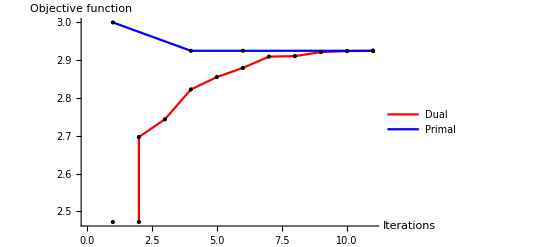

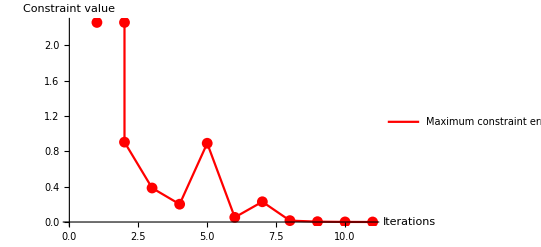

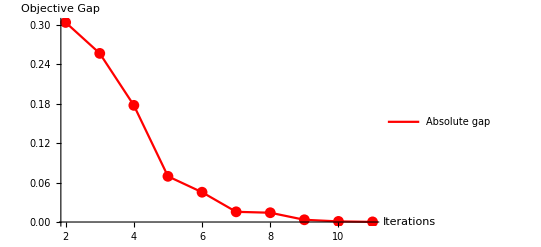

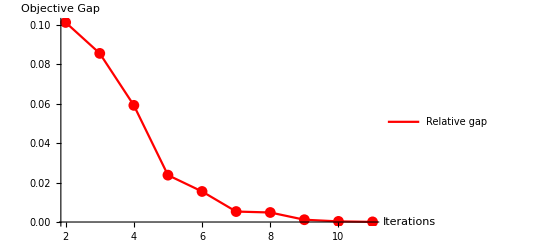

```mathematica
ListPlot[{GetStats["ObjectiveValues"],GetStats["PrimalObjectiveValues"]},PlotStyle->{Red,Blue},MeshStyle->Directive[PointSize[Medium],Black],Joined->True,Mesh->All,PlotLegends->Placed[{"Dual","Primal"},Below],AxesLabel->{"Iterations","Objective function"}]
ListPlot[GetStats["MaxNonlinearConstraintValues"],PlotStyle->Red,Joined->True,Mesh->All,PlotLegends->Placed[{"Maximum constraint error"},Below],AxesLabel->{"Iterations","Constraint value"}]
ListPlot[GetStats["AbsoluteGaps"],PlotStyle->Red,Joined->True,Mesh->All,PlotLegends->Placed[{"Absolute gap"},Below],AxesLabel->{"Iterations","Objective Gap"}]
ListPlot[GetStats["RelativeGaps"],PlotStyle->Red,Joined->True,Mesh->All,PlotLegends->Placed[{"Relative gap"},Below],AxesLabel->{"Iterations","Objective Gap"}]
```

## Entering an optimization problem manually

It is also of course possible to enter an optimization problem manually. The following problem is from the paper mentioned above:

```mathematica
Clear[x1,x2,objective,constraints,variables];
objective = -x1 -x2;
constraints = 
{0.15(x1-8)^2+0.1(x2-6)^2+0.025*Exp[x1]*x2^(-2)-5≤0,
1/x1+1/x2-x1^0.5 x2^0.5 +4≤0,
2x1-3x2-2≤0,
1≤x1≤20,
1≤x2≤20,
x2 ∈ Integers
};
variables = {x1,x2};
```

Now this problem can be solved as

```mathematica
SHOT`SolveMINLP[{objective,constraints},variables,"min",ConstraintToleranceLP->0.5]//AbsoluteTiming
```

{0.84208,{-20.9036,{x1→8.90362,x2→12.}}}

Now we can illustrate the feasible region of the problem above, e.g., using the code below:

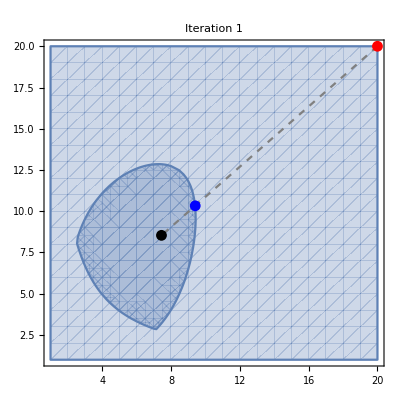
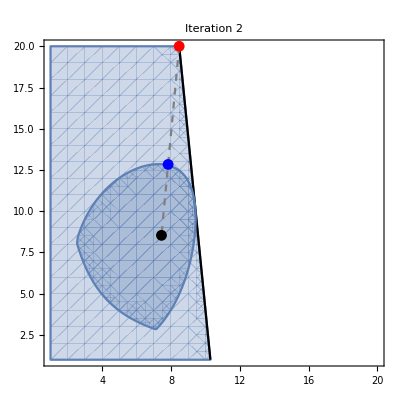
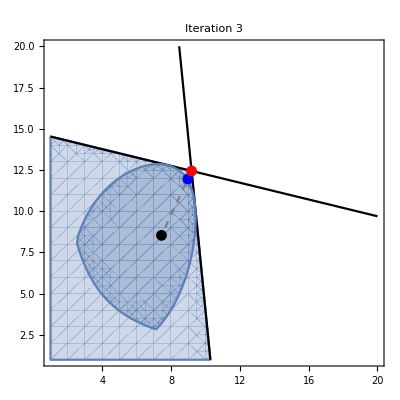
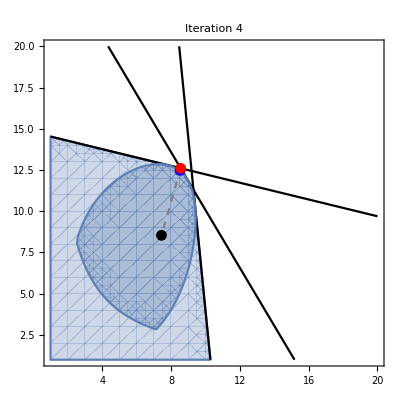
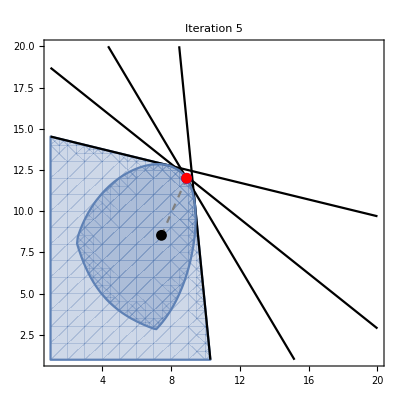
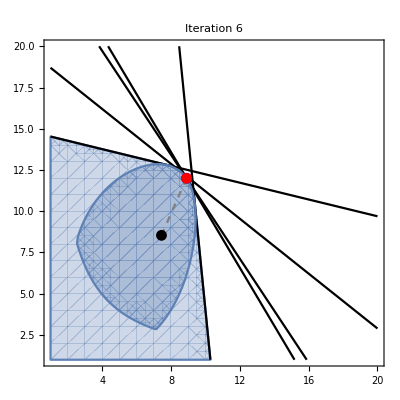

```mathematica
interiorPoint = GetStats["InteriorPoints"];
solutionPoints = GetStats["SolutionPoints"];
hyperplanes=GetStats["Hyperplanes"];
hyperplanePoints=GetStats["HyperplanePoints"];

solPts = Table[variables/.solutionPoints[[i,2]],
{i,1,Length[solutionPoints]}];
hpPts = Join[Table[variables/.hyperplanePoints[[i,2]],
{i,1,Length[hyperplanePoints]}],{{Infinity,Infinity}}];
plotSolPts=Table[ListPlot[{solPts[[i]]}],
{i,1,Length[solPts]}];
plotHpPts=Table[ListPlot[{hpPts[[i]]}],
{i,1,Length[hpPts]}];
nonlinRegion=constraints[[1]]&&constraints[[2]];
plotNonlinRegion = RegionPlot[Evaluate[nonlinRegion],{x1,1,20},{x2,1,20}];
Table[
hpExprs=ReplaceAll[Select[hyperplanes,#[[1]]<iteration&][[All,2]],LessEqual->Equal];
hpRegion=And@@Select[hyperplanes,#[[1]]<iteration&][[All,2]];
Show[
RegionPlot[Evaluate[hpRegion],{x1,1,20},{x2,1,20},PlotLabel->StringJoin["Iteration ",ToString[iteration]]],
ContourPlot[Evaluate[hpExprs],{x1,1,20},{x2,1,20},ContourStyle->Black],
plotNonlinRegion,
ListPlot[{solPts[[iteration]],interiorPoint[[1]]},PlotStyle->Directive[Gray,Dashed],Joined->True],
ListPlot[interiorPoint,PlotStyle->Directive[Large,Black]],
ListPlot[{hpPts[[iteration]]},PlotStyle->Directive[Large,Blue]],
ListPlot[{solPts[[iteration]]},PlotStyle->Directive[Large,Red]]],{iteration,1,Length[solPts]}]
```

By setting the option Strategy to “ECP” cutting planes are generated in the iteration solution points, and no line search is performed. In this case, a lot more iterations are needed:

```mathematica
SHOT`SolveMINLP[{objective,constraints},variables,"min",ConstraintToleranceLP->0.5,Strategy->"ECP"]//AbsoluteTiming
solutionPoints = GetStats["SolutionPoints"];
hyperplanes=GetStats["Hyperplanes"];
hyperplanePoints=GetStats["HyperplanePoints"];
```

Part::partw: Part 1 of {} does not exist.

{1.0261,{-20.9036,{x1→8.90362,x2→12.}}}

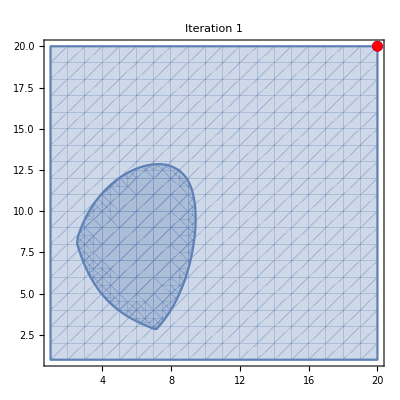
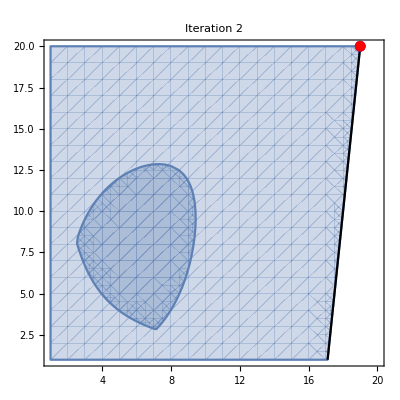
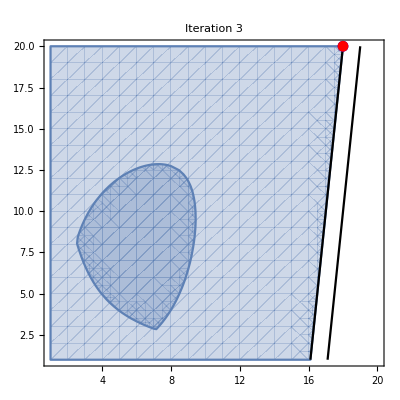
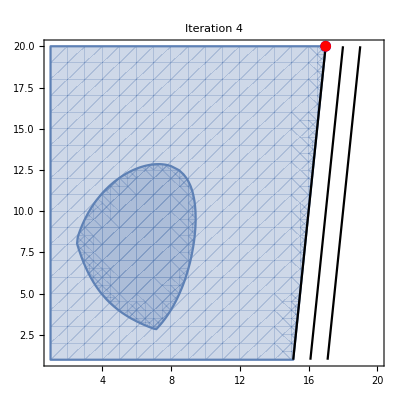
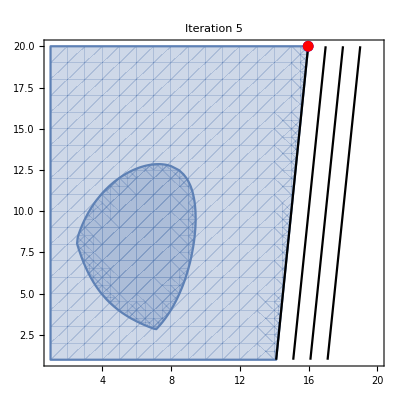
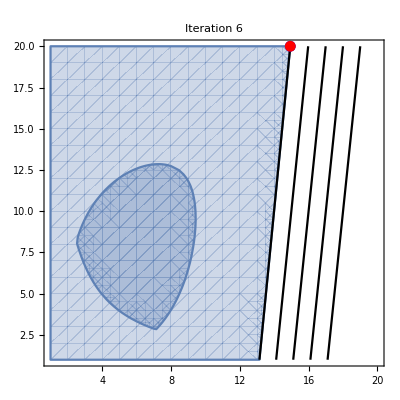
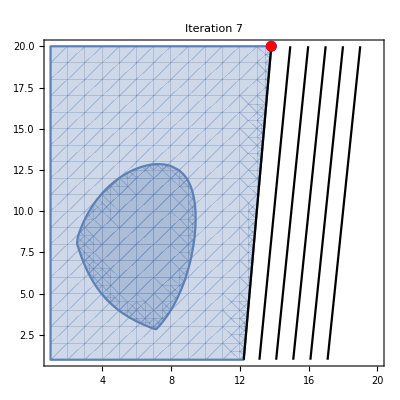
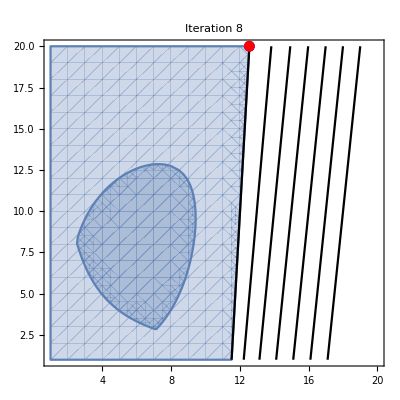

```mathematica
solPts = Table[variables/.solutionPoints[[i,2]],
{i,1,Length[solutionPoints]}];
hpPts = Join[Table[variables/.hyperplanePoints[[i,2]],
{i,1,Length[hyperplanePoints]}],{{Infinity,Infinity}}];
plotSolPts=Table[ListPlot[{solPts[[i]]}],
{i,1,Length[solPts]}];
plotHpPts=Table[ListPlot[{hpPts[[i]]}],
{i,1,Length[hpPts]}];
nonlinRegion=constraints[[1]]&&constraints[[2]];
plotNonlinRegion = RegionPlot[Evaluate[nonlinRegion],{x1,1,20},{x2,1,20}];
Table[
hpExprs=ReplaceAll[Select[hyperplanes,#[[1]]<iteration&][[All,2]],LessEqual->Equal];
hpRegion=And@@Select[hyperplanes,#[[1]]<iteration&][[All,2]];
Show[
RegionPlot[Evaluate[hpRegion],{x1,1,20},{x2,1,20},PlotLabel->StringJoin["Iteration ",ToString[iteration]]],
ContourPlot[Evaluate[hpExprs],{x1,1,20},{x2,1,20},ContourStyle->Black],
plotNonlinRegion,
ListPlot[{hpPts[[iteration]]},PlotStyle->Directive[Large,Blue]],
ListPlot[{solPts[[iteration]]},PlotStyle->Directive[Large,Red]]],{iteration,1,Length[solPts]}]
```

## Solver options

The available solver options are briefly introduced below:

#### ConstraintToleranceLP

This sets the termination constraint tolerance for the LP preprocessing step. When the maximal error for a nonlinear constraint in the solution obtained in an LP step is below this tolerance, the integer restrictions on variables are activated. Default: 0.01

#### ConstraintToleranceMILP

This sets the final termination constraint tolerance for the MILP preprocessing step. When the maximal error for a nonlinear constraint in the solution obtained in an MILP step is below this tolerance, the solver terminates. Default: 0.0001

#### AbsoluteGapTolerance

If a primal bound (valid solution) has been found using an NLP call, the MILP iterations are terminated if the absolute difference between the primal (NLP) and dual (MILP) objective values are below this tolerance. Default: 0.0001

#### RelativeGapTolerance

If a primal bound (valid solution) has been found using an NLP call, the MILP iterations are terminated if the relative difference between the primal (NLP) and dual (MILP) objective values are below this tolerance. The relative objective value is calculated as the absolute difference between the primal and dual objective divided with a small value (10^-10) added to the primal objective value. Default: 0.0001

#### MinimaxAccuracyGoal and MinimaxPrecisionGoal

These parameters are passed on to Mathematica’s FindMaximum function used to find the interior point. Default: 6

#### MaximalIterationsLP and MaximalIterationsMILP

These determines the maximum number of LP and MILP iterations before terminating. Default: 20 and 40

#### Strategy

This parameter determines the main strategy used by the solver. Options are “ESH” or “ECP”. If ECP is used, no line search is performed, and a cutting plane is generated instead of a supporting hyperplane. Default: “ESH”

#### PrimalBoundNLPIterationGap

This parameter determines how often an NLP problem is solved with the integer solution values fixed, which is used to find a primal solution to the problem. A value of -1 means that no NLP problems are solved, and a value of 1 means that a NLP problem is solved after each MILP iteration, 2 solves an NLP problem every second iteration, and so on.  Default: 5

#### RootMethod

Determines what solution method to use for the line search. Options are “FindRoot” or “Bisection”. FindRoot uses Mathematica’s builtin function with the same name, whereas Bisection uses a tailor-made implementation based on bisection. Default: “Bisection”

#### InteriorPointStrategy

Determines what solution method to use when searching for an interior point. Options are “Minimax” or “CuttingPlane”. Minimax uses Mathematica’s builtin functions, whereas CuttingPlane uses a tailor-made implementation based on a cutting plane strategy. Default: “Minimax”

#### ShowProblemSummary

Prints out the optimization problem to the Messages-notebook during runtime. Default: False

#### UsePrimalBoundCut

Adds a constraint that cuts away an objective with values worse than a known primal bound. Default: True

#### ConstraintToleranceConstant

A small positive constant added to the RHS of the generated supporting hyperplane or cutting plane. This is used to prevent solutions being cut of by Mathematica’s linear solver. Default: 10^-9

#### NegativeNonlinearObjectiveBound and PositiveNonlinearObjectiveBound

If an optimization problem has a nonlinear objective function, it is rewritten as an auxilliary objective function constraint consisting of the objective function minus an additional variable that is minimized in the new objective. These parameters are used to set the bounds for this objective function variable. Using too loose values may cause problems for the NLP solver when finding an interior point, and using too strict values may restrict the solution of the problem. Default: -10^5 and  10^5